## FASE 0

```mathematica
a=Get[NotebookDirectory[]<>"simulazione_0video.txt"];
```

-Graphics3D-

-Graphics3D-

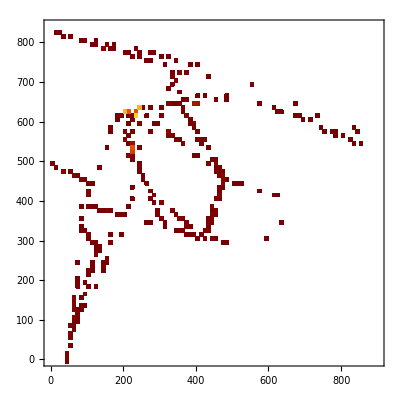

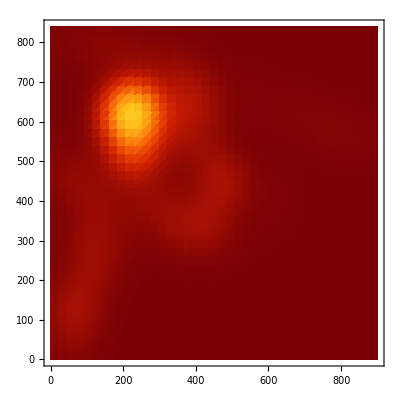

```mathematica
a1=Histogram3D[a,10,PlotRange->{{0,900},{0,840},{0,Automatic}},ColorFunction->"SolarColors"]
a2=SmoothHistogram3D[a,PlotRange->{{0,900},{0,840},Automatic},PlotStyle->{Directive[ColorFunction->"SolarColors",Opacity[.5]]}]
a3= DensityHistogram[a,100,PlotRange->{{0,900},{0,840}}, ColorFunction->"SolarColors"]
a4= SmoothDensityHistogram[a,50,PlotRange->{{0,900},{0,840}}, ColorFunction->"SolarColors"]
```

```mathematica
img1=Import[NotebookDirectory[]<>"00-FASE0_a.jpg"]
```

-Graphics-

```mathematica
altezza=-0.5;
mappa=Graphics3D[{Texture[img1],Polygon[{{900,0,altezza},{0,0,altezza},{0,840,altezza},{900,840,altezza}},VertexTextureCoordinates->{{0,0},{-1,0},{-1,1},{0,1}}](*,
Lighting->"Neutral"*)}, ImageSize->800]
```

-Graphics3D-

```mathematica
Show[a2,mappa,PlotRange->{{0,900},{0,840},{-1,0.000001}},ImageSize->800]
```

-Graphics3D-

```mathematica
Show[img1,a3]
```

-Graphics-

```mathematica
Show[a4,img1]
```

-Graphics-

```mathematica
img2=img1
```

-Graphics-

```mathematica
u=RemoveBackground[img2,{"Background",White}]
```

-Graphics-

```mathematica
Show[a4,u, ImageSize->800]
```

-Graphics-

## FASE 1

```mathematica
b=Get[NotebookDirectory[]<>"simulazione_1video.txt"];
```

-Graphics3D-

-Graphics3D-

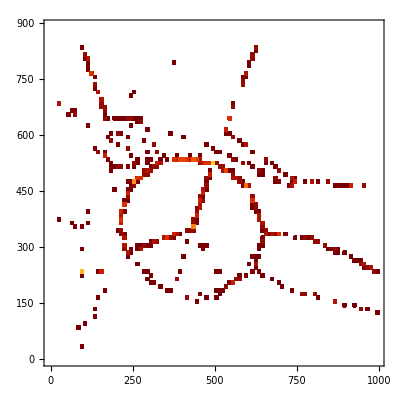

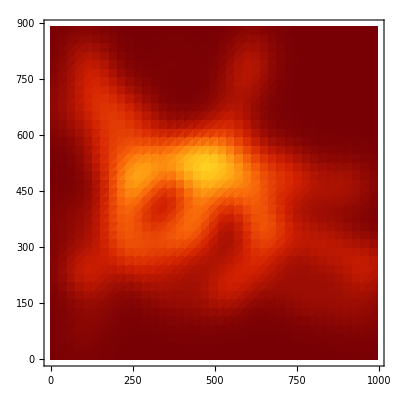

```mathematica
b1=Histogram3D[b,10,PlotRange->{{0,995},{0,890},{0,Automatic}},ColorFunction->"SolarColors"]
b2=SmoothHistogram3D[b,PlotRange->{{0,995},{0,890},Automatic},PlotStyle->{Directive[ColorFunction->"SolarColors",Opacity[.5]]}]
b3= DensityHistogram[b,100,PlotRange->{{0,995},{0,890}}, ColorFunction->"SolarColors"]
b4= SmoothDensityHistogram[b,50,PlotRange->{{0,995},{0,890}}, ColorFunction->"SolarColors"]
```

```mathematica
img2=Import[NotebookDirectory[]<>"00-FASE1_a.jpg"]
```

-Graphics-

```mathematica
altezza=-0.5;
mappa2=Graphics3D[{Texture[img2],Polygon[{{995,0,altezza},{0,0,altezza},{0,890,altezza},{995,890,altezza}},VertexTextureCoordinates->{{0,0},{-1,0},{-1,1},{0,1}}](*,
Lighting->"Neutral"*)}]
```

-Graphics3D-

```mathematica
Show[b2,mappa2,PlotRange->{{0,995},{0,890},{-1,0.000001}},ImageSize->800]
```

-Graphics3D-

```mathematica
Show[img2,b3]
```

-Graphics-

```mathematica
Show[b4,img2]
```

-Graphics-

```mathematica
img3=img2
```

-Graphics-

```mathematica
u1=RemoveBackground[img3,{"Background",White}]
```

-Graphics-

```mathematica
Show[b4,u1,ImageSize->800]
```

-Graphics-